I’m trying to compare John’s Gillespie algorithm against one I found online (https://www.r-bloggers.com/vanilla-c-code-for-the-stochastic-simulation-algorithm/) to see if there’s a problem with my code.

Here is the predator-prey model they use. This model has density-dependence in both birth and death rates, such that birth rates decrease and death rates increase as the population size increases. 

I’m additionally assuming that prey reproductive rate evolves in a trade-off with predation rate: the higher the reproductive rate, the higher the predation rate (a’(b) > 0). In order for there to be an ESS, I would guess that a’’(b) > 0 as well.

```mathematica
dc=b c-d c-(b-d) c^2/K-a[b] c p
dp=e a[b] c p-m p
db=V Simplify[D[dc/c,b]]
```

b c-c d-(c^2 (b-d))/K-c p a[b]

-m p+c e p a[b]

V (1-c/K-p a'[b])

The easiest way for me to check that intuition is using an adaptive dynamics approach:

```mathematica
dc=b c-d c-(b-d) (c+cm)^2/K-a[b] c p
dp=e (a[b] c+a[bm] cm) p-m p
dcm=bm cm-d cm-(bm-d) (c+cm)^2/K-a[bm] cm p
```

b c-c d-((c+cm)^2 (b-d))/K-c p a[b]

-m p+e p (c a[b]+cm a[bm])

bm cm-cm d-((c+cm)^2 (bm-d))/K-cm p a[bm]

```mathematica
MatrixForm[J=D[{dc,dp,dcm},{{c,p,cm}}]]
MatrixForm[J/.{cm->0}]
```

(b-d-(2 (c+cm) (b-d))/K-p a[b] | -c a[b] | -(2 (c+cm) (b-d))/K
e p a[b] | -m+e (c a[b]+cm a[bm]) | e p a[bm]
-(2 (c+cm) (bm-d))/K | -cm a[bm] | bm-d-(2 (c+cm) (bm-d))/K-p a[bm])

(b-d-(2 c (b-d))/K-p a[b] | -c a[b] | -(2 c (b-d))/K
e p a[b] | -m+c e a[b] | e p a[bm]
-(2 c (bm-d))/K | 0 | bm-d-(2 c (bm-d))/K-p a[bm])

Mutant can invade if

```mathematica
bm-d-(2 c (bm-d))/K-p a[bm]>0;
```

This is the invasion fitness. Calculating the fitness gradient:

```mathematica
fitgrad=D[bm-d-(2 c (bm-d))/K-p a[bm],bm]/.{bm->b}
```

1-(2 c)/K-p a'[b]

And evaluating at the mutant-free equilibrium:

```mathematica
Solve[{(dc/.cm->0)==0,(dp/.cm->0)==0},{c,p}]
```

{{c→m/(e a[b]),p→((b-d) (-m+e K a[b]))/(e K a[b]^2)},{c→0,p→0},{c→K,p→0}}

```mathematica
FullSimplify[fitgrad/.{c->m/(e a[b]),p->((b-d) (-m+e K a[b]))/(e K a[b]^2)}]
```

(-2 m a[b]+e K a[b]^2+(b-d) (m-e K a[b]) a'[b])/(e K a[b]^2)

You can see that there will be a singular strategy (a zero of this equation). Will that be an ESS? Only if a’’(b) > 0, as expected.

```mathematica
D[bm-d-(2 c (bm-d))/K-p a[bm],{bm,2}]/.{bm->b}
```

-p a''[b]

Okay, then what would the ESS be if a(b) = a_0 b^2?

```mathematica
Solve[(FullSimplify[fitgrad/.{c->m/(e a[b]),p->((b-d) (-m+e K a[b]))/(e K a[b]^2)}]/.{a[b]->a0 b^2, a'[b]->2 a0 b})==0,b]
```

{{b→1/3 (2 d-(4 a0 d^2 e K)/(-8 a0^3 d^3 e^3 K^3+27 a0^2 d e^2 K^2 m+3 √3 √(-16 a0^5 d^4 e^5 K^5 m+27 a0^4 d^2 e^4 K^4 m^2))^(1/3)-1/(a0 e K)(-8 a0^3 d^3 e^3 K^3+27 a0^2 d e^2 K^2 m+3 √3 √(-16 a0^5 d^4 e^5 K^5 m+27 a0^4 d^2 e^4 K^4 m^2))^(1/3))},{b→(2 d)/3+(2 (1+ⅈ √3) a0 d^2 e K)/(3 (-8 a0^3 d^3 e^3 K^3+27 a0^2 d e^2 K^2 m+3 √3 √(-16 a0^5 d^4 e^5 K^5 m+27 a0^4 d^2 e^4 K^4 m^2))^(1/3))+1/(6 a0 e K)(1-ⅈ √3) (-8 a0^3 d^3 e^3 K^3+27 a0^2 d e^2 K^2 m+3 √3 √(-16 a0^5 d^4 e^5 K^5 m+27 a0^4 d^2 e^4 K^4 m^2))^(1/3)},{b→(2 d)/3+(2 (1-ⅈ √3) a0 d^2 e K)/(3 (-8 a0^3 d^3 e^3 K^3+27 a0^2 d e^2 K^2 m+3 √3 √(-16 a0^5 d^4 e^5 K^5 m+27 a0^4 d^2 e^4 K^4 m^2))^(1/3))+1/(6 a0 e K)(1+ⅈ √3) (-8 a0^3 d^3 e^3 K^3+27 a0^2 d e^2 K^2 m+3 √3 √(-16 a0^5 d^4 e^5 K^5 m+27 a0^4 d^2 e^4 K^4 m^2))^(1/3)}}

There is an ESS here, even if it is ugly.

Specify this as the model to use:

```mathematica
Clear[V]
```

(c-c^2/K-2 a0 b c p)/c

```mathematica
dc=b c-d c-(b-d) c^2/K-a0 b^2 c p
dp=e a0 b^2 c p-m p
db=V Simplify[D[dc/c,b]]
```

b c-c d-(c^2 (b-d))/K-a0 b^2 c p

a0 b^2 c e p-m p

(1-c/K-2 a0 b p) V

Specify some parameters for a non-evolving case, just to see where that gets us. I’m going to use the parameters from https://www.r-bloggers.com/vanilla-c-code-for-the-stochastic-simulation-algorithm/

```mathematica
params={K->2000,a0->0.000125,e->5,m->2.5, d->1}
params0={K->2000,a0->0.000125,e->5,m->2.5, d->1,b->2}
```

{K→2000,a0→0.000125,e→5,m→2.5,d→1}

{K→2000,a0→0.000125,e→5,m→2.5,d→1,b→2}

Simulating from the initial condition on that site, you can see that you are starting at the equilibrium, so the system shouldn’t move too much.

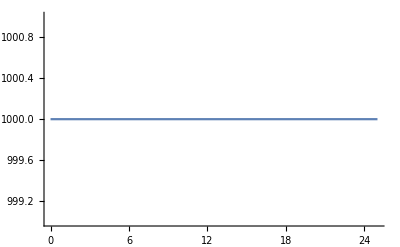

-Graphics-

```mathematica
out=NDSolve[{c'[t]==(dc/.{c->c[t],p->p[t]}/.params0),
p'[t]==(dp/.{c->c[t],p->p[t]}/.params0),
c[0]==1000,p[0]==1000},{c[t],p[t]},{t,0,25}];
Plot[c[t]/.out,{t,0,25},PlotRange->All]
Plot[p[t]/.out,{t,0,25},PlotRange->All]
```

What if you let b evolve and start the system away from the equilibrium?

Here is what the equilibrium should be:

```mathematica
Solve[{dc==0,dp==0,db==0}/.params,{c,p,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→2000.,p→0.},{c→2000.,p→0.,b→-1.41421},{c→2000.,p→0.,b→1.41421},{c→1000.,p→1000.,b→2.}}

```mathematica
params={K->500,a0->0.0005,e->5,m->4, d->1};
Table[Solve[{dc==0,dp==0,db==0}/.{K->500,e->5,m->4, d->1},{c,p,b}][[4]],{a0,0.001,0.004,0.0005}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

{{c→200.,p→150.,b→2.},{c→133.333,p→122.222,b→2.},{c→100.,p→100.,b→2.},{c→80.,p→84.,b→2.},{c→66.6667,p→72.2222,b→2.},{c→57.1429,p→63.2653,b→2.},{c→50.,p→56.25,b→2.}}

```mathematica
300/8
```

75/2

```mathematica
db
```

(1-c/K-2 a0 b p) V

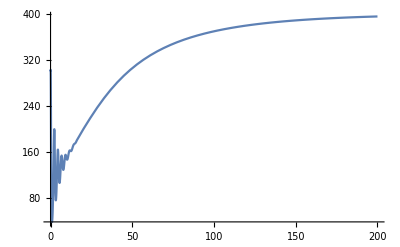

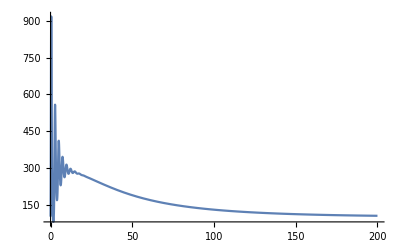

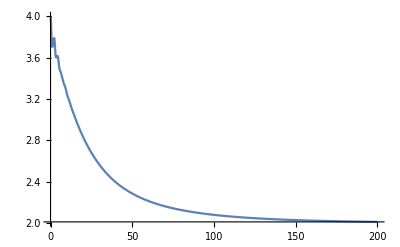

```mathematica
params={K->500,a0->0.0005,e->5,m->4, d->1};
out=NDSolve[{c'[t]==(dc/.{c->c[t],p->p[t],b->b[t]}/.params),
p'[t]==(dp/.{c->c[t],p->p[t],b->b[t]}/.params),
b'[t]==(db/.{c->c[t],p->p[t],b->b[t]}/.params/.V->0.21),
c[0]==300,p[0]==101,b[0]==4},{c[t],p[t],b[t]},{t,0,500}];
Plot[c[t]/.out,{t,0,200},PlotRange->All]
Plot[p[t]/.out,{t,0,200},PlotRange->All]
Plot[b[t]/.out,{t,0,200},PlotRange->All]
```

```mathematica
Integrate[1/(Linf W^(2/3)-W),W]
```

-3 Log[-Linf+W^(1/3)]

```mathematica
Solve[{dc==0,dp==0,db==0},{c,p,b}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→K,p→0},{c→m/(4 a0 d^2 e),p→-(-4 a0 d^2 e K+m)/(16 a0^2 d^3 e K),b→2 d},{c→K,p→0,b→-(√m)/(√a0 √e √K)},{c→K,p→0,b→(√m)/(√a0 √e √K)}}

```mathematica
Eigenvalues[D[{dc,dp,db},{{c,p,b}}]/.{c->m/(4 a0 d^2 e),p->-(-4 a0 d^2 e K+m)/(16 a0^2 d^3 e K),b->2 d}/.params/.V->0.1]
```

{-0.251159+0.698588 ⅈ,-0.251159-0.698588 ⅈ,-0.0226816+0. ⅈ}

```mathematica
params={K->500,a0->0.002,e->5,m->4, d->1};
Solve[{dc==0,dp==0,db==0}/.params,{c,p,b}]
Solve[db==0,b]/.params/.c->131/.p->113
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→500.,p→0.},{c→500.,p→0.,b→-0.894427},{c→500.,p→0.,b→0.894427},{c→100.,p→100.,b→2.}}

{{b→1.63274}}

Here is a simulation away from that.

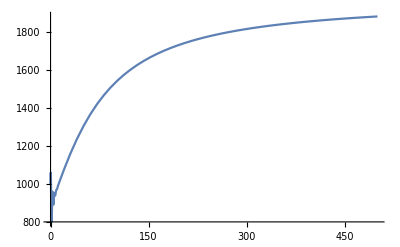

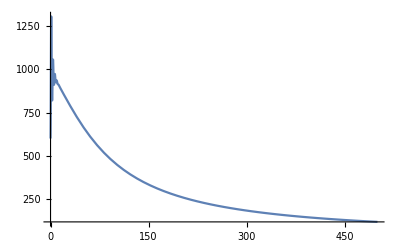

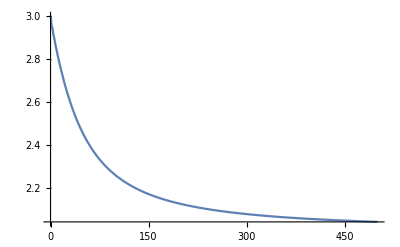

```mathematica
out=NDSolve[{c'[t]==(dc/.{c->c[t],p->p[t],b->b[t]}/.params),
p'[t]==(dp/.{c->c[t],p->p[t],b->b[t]}/.params),
b'[t]==(db/.{c->c[t],p->p[t],b->b[t]}/.params/.V->0.1),
c[0]==1000,p[0]==600,b[0]==3},{c[t],p[t],b[t]},{t,0,500}];
Plot[c[t]/.out,{t,0,500},PlotRange->All]
Plot[p[t]/.out,{t,0,500},PlotRange->All]
Plot[b[t]/.out,{t,0,500},PlotRange->All]
```

Don’t start too far away though, or the whole system will collapse dramatically!

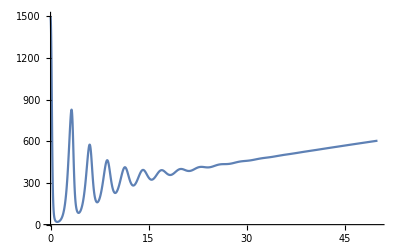

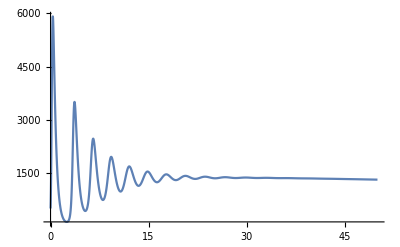

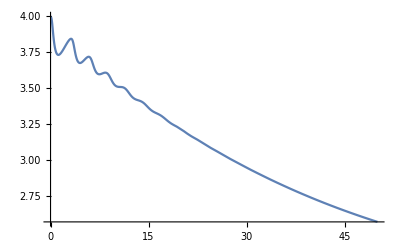

```mathematica
out=NDSolve[{c'[t]==(dc/.{c->c[t],p->p[t],b->b[t]}/.params),
p'[t]==(dp/.{c->c[t],p->p[t],b->b[t]}/.params),
b'[t]==(db/.{c->c[t],p->p[t],b->b[t]}/.params/.V->0.1),
c[0]==1500,p[0]==500,b[0]==4},{c[t],p[t],b[t]},{t,0,500}];
Plot[c[t]/.out,{t,0,50},PlotRange->All]
Plot[p[t]/.out,{t,0,50},PlotRange->All]
Plot[b[t]/.out,{t,0,50},PlotRange->All]
```

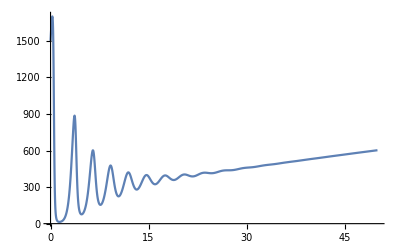

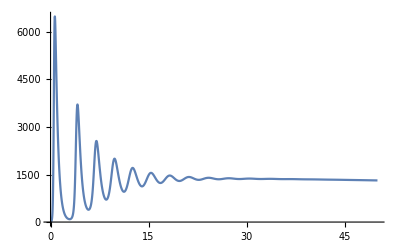

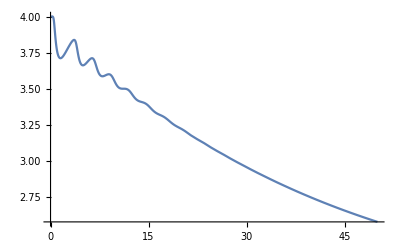

```mathematica
out=NDSolve[{c'[t]==(dc/.{c->c[t],p->p[t],b->b[t]}/.params),
p'[t]==(dp/.{c->c[t],p->p[t],b->b[t]}/.params),
b'[t]==(db/.{c->c[t],p->p[t],b->b[t]}/.params/.V->0.1),
c[0]==1500,p[0]==5,b[0]==4},{c[t],p[t],b[t]},{t,0,500}];
Plot[c[t]/.out,{t,0,50},PlotRange->All]
Plot[p[t]/.out,{t,0,50},PlotRange->All]
Plot[b[t]/.out,{t,0,50},PlotRange->All]
```

```mathematica
dc=b c-d c-(b-d) c^2/K-a0 b^2 c p
dp=e a0 b^2 c p-m p
db=V Simplify[D[dc/c,b]]
```

There was an issue that cropped up with this model: basically, it’s inherent tendency to oscillate makes for disastrous consequences for a stochastic simulation. But we can rectify that by figuring out how to minimize the tendency to oscillate.

Here the ecology-only model - let’s focus there. Note that I’m going to ignore the effects of b on attack rate.

```mathematica
dc=b c-d c-(b-d) c^2/K-a[b] c p
dp=e a[b]c p-m p
```

b c-c d-(c^2 (b-d))/K-c p a[b]

-m p+c e p a[b]

Let’s nondimensionalize to make the math easier to see, keeping mind that b will actually be changing (and changing a along with it).

```mathematica
Simplify[(dc that/xhat)/.{c->X xhat,p->Y yhat}/.{xhat->K,that->1/m,yhat->m/a[b]}]==(b-d)/m X(1-X)-X Y//Simplify
Simplify[(dp that/yhat)/.{c->X xhat,p->Y yhat}/.{xhat->K,that->1/m,yhat->m/a[b]}]
```

True

Y (-1+(e K X a[b])/m)

Here’s the dimensionless model

```mathematica
dX=(b-d)/m X(1-X)-X Y
dY=Y (-1+(e K X a[b])/m)
(* define the dimensionless parameters r[b]=(b-d)/m and k[b] = e K a[b]/m *)
dX=r[b] X(1-X)-X Y
dY=Y (-1+X k[b])
```

((b-d) (1-X) X)/m-X Y

Y (-1+(e K X a[b])/m)

-X Y+(1-X) X r[b]

Y (-1+X k[b])

```mathematica
(* Equilibria *)
Solve[{dX==0,dY==0},{X,Y}]//Simplify
```

{{X→1/k[b],Y→((-1+k[b]) r[b])/k[b]},{X→0,Y→0},{X→1,Y→0}}

```mathematica
Assuming[k[b]>0,Simplify[Eigenvalues[D[{dX,dY},{{X,Y}}]]/.{X->1/k[b],Y->((-1+k[b]) r[b])/k[b]}]]
```

{-(r[b]+√(r[b] (4 k[b]-4 k[b]^2+r[b])))/(2 k[b]),(-r[b]+√(r[b] (4 k[b]-4 k[b]^2+r[b])))/(2 k[b])}

For a feasible equilibrium, we require that k[b] > 1 (e a[b] K > m). 
For stability we require that k[b] > 1 as well.

```mathematica
4 k[b]-4 k[b]^2+r[b]<r[b] (* this ensures that the term under the square root is smaller than r[b]^2 *)
4 k[b]-4 k[b]^2<0
4 k[b]<4 k[b]^2
k[b]>1
```

There will be no oscillations if

```mathematica
4 k[b]-4 k[b]^2+r[b]>0
r[b]-4 k[b] (k[b]-1)>0
```

```mathematica
(b-d)/m-4 (e a[b] K)/m ((e a[b] K)/m-1)>0
```

To keep oscillations down, we want e a[b] K/m to be close to 1. That should really make a big difference.

```mathematica
params={K->250,a0->0.001,e->5,m->4, d->1};
Solve[{dc==0,dp==0,db==0}/.params,{c,p,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→250.,p→0.},{c→250.,p→0.,b→-1.78885},{c→250.,p→0.,b→1.78885},{c→200.,p→50.,b→2.}}

However, there is a problem there: the prey equilibrium is 1/k(b), so the closer k(b) gets to 1, the closer the prey equilibrium gets to its maximum. I guess that’s okay, it just means we cannot vary only a single parameter. We need to vary multiple parameters.

```mathematica
(* What if you cull the predator population *)
Solve[dc==0,c]
Solve[(D[dc/c,b]/.c->-(K (-b+d+a0 b^2 p))/(b-d))==0,b]
```

{{c→0},{c→-(K (-b+d+a0 b^2 p))/(b-d)}}

{{b→0},{b→2 d}}

```mathematica
(* what if you cull the prey population? *)
(* then the predator population will either decline to extinction (if the per-capita growth rate is < 0) or it will blow up to infinity (if the per-capita growth rate is > 0) *)
```

```mathematica
dp
```

-m p+c e p a[b]

```mathematica
Solve[dp==0,p]
```

{{p→0}}

```mathematica
Solve[D[dc/c,b]==0,b]
```

{{b→(-c+K)/(2 a0 K p)}}